```mathematica
(* This notebook solves and simulates the TractableBufferStock model *)
```

```mathematica
(* This cell is basically housekeeping and setup stuff; it can be ignored *)
ClearAll["Global`*"];ParamsAreSet=False;
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[$VersionNumber<6,(*then*) Print["These programs require Mathematica version 6 or greater."];Abort[]];
(* If running from shell, must start from inside same directory in which notebook resides *)
AutoLoadDir=SetDirectory["../../CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
TractableFigDir=SetDirectory[rootDir<>"/Examples/TractableBufferStock/Figures/"];
TractableCodeDir=SetDirectory[rootDir<>"/Examples/TractableBufferStock"];
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;
```

Solving ...

Below 𝓂MinPermitted after 43 backwards Euler iterations.

Last 2 Points:(1.80841 | 0.593991 | 0.20245 | -17.0137 | -0.0737916
1.25759 | 0.468788 | 0.257575 | -18.9731 | -0.13305)

Solving ...

Above 𝓂MaxPermitted after 68 backwards Euler iterations.

Last 2 Points:(21.4377 | 2.45831 | 0.0737605 | -6.21838 | -0.000637774
22.4767 | 2.53461 | 0.0731271 | -6.05163 | -0.000582708)

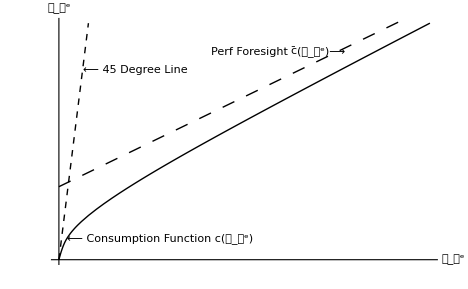

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/TractableBufferStockcFunc.xxx

```mathematica
StableArmStyle={Black,Dashing[{.01}],Thickness[Medium]};
Get[TractableCodeDir<>"/cFunc.m"];
ExportFigsToDir["TractableBufferStockcFunc",TractableFigDir];
```

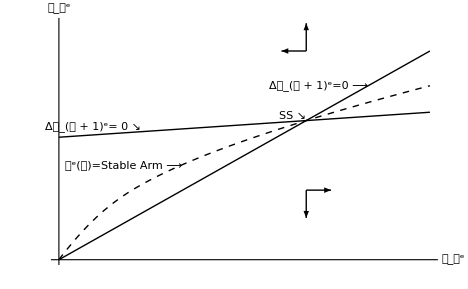

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/TractableBufferStockPhaseDiag.xxx

```mathematica
Get[TractableCodeDir <> "/PhaseDiag.m"];
ExportFigsToDir["TractableBufferStockPhaseDiag",TractableFigDir];
```

Solving ...

Below 𝓂MinPermitted after 43 backwards Euler iterations.

Last 2 Points:(1.80841 | 0.593991 | 0.20245 | -17.0137 | -0.0737916
1.25759 | 0.468788 | 0.257575 | -18.9731 | -0.13305)

Solving ...

Above 𝓂MaxPermitted after 68 backwards Euler iterations.

Last 2 Points:(21.4377 | 2.45831 | 0.0737605 | -6.21838 | -0.000637774
22.4767 | 2.53461 | 0.0731271 | -6.05163 | -0.000582708)

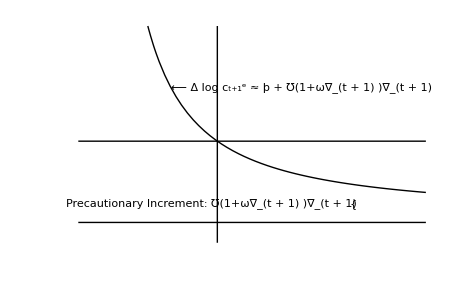

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/TractableBufferStockGrowthA.xxx

-Graphics-

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;
HorizAxis=((r)-ϑ)/ρ-0.01;
𝒸GroMax=Log[𝒞tp1O𝒞t[0.5 𝓂E]];
BufferFigPlot=Show[Plot[Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂E,2.5 𝓂E}
,Ticks->{{{𝓂E,"(𝓂̌)^e"}},{{𝔤+℧,"γ"},{((r)-ϑ)/ρ,Style["ρ^-1(r-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,2.5 𝓂E},{HorizAxis,𝒸GroMax}}
]
(*,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMax}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMax}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,𝔤+℧},{2.5 𝓂E,𝔤+℧}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.5 𝓂E,((r)-ϑ)/ρ}}]}
,PlotRange->{{0,2.5 𝓂E},{HorizAxis,𝒸GroMax}}
]
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
];
(* The thorn character þ does not appear properly unless encoded with the WindowsANSI encoding, which necessitates the cumbersome apparatus below *)
cLev=Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"];
cELevtp1=SubsuperscriptBox[cLev,Style["t+1",CharacterEncoding->"WindowsANSI"],Style["e",CharacterEncoding->"WindowsANSI"]] //DisplayForm;
dLog = Style["Δ log ",CharacterEncoding->"WindowsANSI"];
ArrowPointingLeft = Style[" ⟵ ",CharacterEncoding->"WindowsANSI"];
ArrowPointingRight = Style[" ⟶ ",CharacterEncoding->"WindowsANSI"];
ApproxcELevGro = Style[" ≈ þ + ℧(1+ω∇_(t + 1) )∇_(t + 1) ",CharacterEncoding->"WindowsANSI"];
TractableBufferStockGrowthA=BufferFigBaseline=Show[BufferFigPlot
,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cELevtp1,ApproxcELevGro}]],{(𝓂E 2)/3,Log[𝒞tp1O𝒞t[(𝓂E 2)/3]]},{-1,0}]]
,Graphics[Text[" {",{𝓂E 2,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)},{1,0}]]
,Graphics[Text["Precautionary Increment: ℧(1+ω∇_(t + 1) )∇_(t + 1)    ",{𝓂E 2,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)},{1,0}]]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉^e","Growth"}
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
,PlotRange->{{((r)-ϑ)/ρ-0.1,2.5 𝓂E},{HorizAxis,𝒸GroMax}}];
ExportFigsToDir["TractableBufferStockGrowthA",TractableFigDir];
TractableBufferStockGrowthA
```

Solving ...

Below 𝓂MinPermitted after 86 backwards Euler iterations.

Last 2 Points:(1.79849 | 0.665853 | 0.216128 | -13.801 | -0.0881375
1.29276 | 0.542761 | 0.276593 | -15.1886 | -0.15875)

Solving ...

Above 𝓂MaxPermitted after 140 backwards Euler iterations.

Last 2 Points:(27.3284 | 3.15255 | 0.0817088 | -4.0021 | -0.000217361
27.9314 | 3.20178 | 0.0815813 | -3.94236 | -0.000205696)

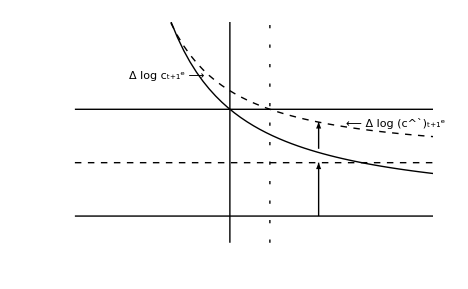

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/TractableBufferStockGrowthB.xxx

```mathematica
r = rBase+.04;
FindStableArm;
cEModLevtp1=SubsuperscriptBox[OverscriptBox[Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"],"`"],Style["t+1",Plain],Style["e",Plain]];
BufferFigNew = Plot[
Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂EBase,2.5 𝓂EBase}
,PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
TractableBufferStockGrowthB=Show[BufferFigPlot
,BufferFigNew
,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cEModLevtp1}]],{(𝓂EBase 14)/8,Log[𝒞tp1O𝒞t[(𝓂EBase 13)/8]]},{-1,0}]]
,Graphics[Text[DisplayForm[RowBox[{dLog, cELevtp1, ArrowPointingRight,"   "}]],{(𝓂EBase 5)/6,Log[𝒞tp1O𝒞t[(𝓂EBase 5)/6]]},{1,1}]]
,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Line[{{𝓂E,HorizAxis},{𝓂E,Log[𝒞tp1O𝒞t[1.5]]}}]}]
,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.5 𝓂EBase,((r)-ϑ)/ρ}}]}]
,PhaseArrow[{𝓂E 1.25,(rBase-ϑ)/ρ},{𝓂E 1.25,((r)-ϑ)/ρ}]
,PhaseArrow[{𝓂E 1.25,Log[𝒞tp1O𝒞t[𝓂E 1.25]]-(((r)-rBase) 2)/(ρ 4)},{𝓂E 1.25,Log[𝒞tp1O𝒞t[𝓂E 1.25]]}]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉","Growth"}
,AxesOrigin->{Automatic,HorizAxis}
,Ticks->{{{𝓂EBase,"m̌"},{𝓂E,"(𝓂̌)^`"}},{{𝔤+℧,"γ"},{(rBase-ϑ)/ρ,
Style["ρ^-1(𝓇-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]},{((r)-ϑ)/ρ,Style["ρ^-1(𝓇^`-ϑ)≈þ^`",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,1.8 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.5𝓂E]]}}];
ExportFigsToDir["TractableBufferStockGrowthB",TractableFigDir];
```

```mathematica
r = rBase;
ϑ=ϑBase-0.02;
FindStableArm;
cFuncPlotNew=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->{Black,Thickness[Medium]}];
cFuncPlotNewPoints=Map[{{#,𝒸[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.01}]];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂MaxMax},PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
Stable𝓂LocusPoints=Map[{{#,𝓂EDelEqZero[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.1}]];
```

Solving ...

Below 𝓂MinPermitted after 65 backwards Euler iterations.

Last 2 Points:(1.89376 | 0.55051 | 0.175541 | -21.4434 | -0.0609188
1.30659 | 0.434501 | 0.224654 | -23.8744 | -0.112912)

Solving ...

Above 𝓂MaxPermitted after 98 backwards Euler iterations.

Last 2 Points:(27.9361 | 2.57181 | 0.060756 | -7.05996 | -0.000351073
28.914 | 2.63106 | 0.060424 | -6.91544 | -0.000328297)

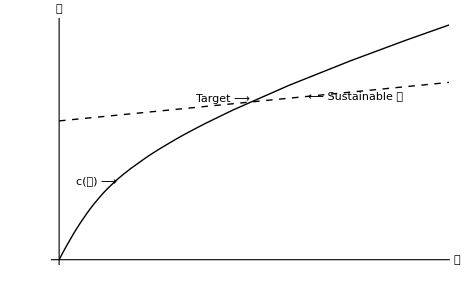

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/TractableBufferStockTarget.xxx

```mathematica
SetOptions[ListPlot,PlotStyle->Black];SimGeneratePath[𝓂EBase,200];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{Black,PointSize[0.008]}];
{𝓂MinNew,𝓂MaxNew}={0,2 𝓂EBase};
{𝒸MinNew,𝒸MaxNew}={0,1.5 𝒸EBase};
TractableBufferStockTarget = Show[cFuncPlotBase,Stable𝓂LocusPlot
,Graphics[Text["Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["     ⟵ Sustainable 𝒸",{1.3 𝓂EBase,𝓂EDelEqZero[1.3 𝓂EBase]},{-1,0}]]
,Graphics[Text["c(𝓂) ⟶   ",{0.3𝓂EBase,0.5𝒸EBase},{1,0}]]
,Ticks->None
,PlotRange->{{𝓂MinNew,𝓂MaxNew},{𝒸MinNew,𝒸MaxNew}}
,AxesLabel->{"𝓂","𝒸"}];
OldAndNewcFuncsPlot = Show[Stable𝓂LocusPlot,cFuncPlotBase,cFuncPlotNew
,PlotRange->{{0,𝓂MaxMax},{0,Automatic}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["TractableBufferStockTarget",TractableFigDir];
```

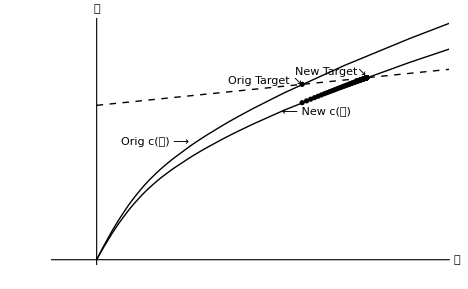

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/PhaseDiagramDecreaseThetaPlot.xxx

-Graphics-

```mathematica
PhaseDiagramDecreaseThetaPlot = Show[OldAndNewcFuncsPlot,𝓂𝒸PathPlot
,Graphics[Text["Orig Target ↘",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["New Target↘ ",{𝓂E,1.03𝒸E},{1,0}]]
,Graphics[Text["Orig c(𝓂) ⟶",{0.45𝓂EBase,0.67𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ New c(𝓂)",{0.9𝓂EBase,cE[0.9𝓂EBase]},{-1,0}]]
,Ticks->None
,AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{𝓂MinNew-1,𝓂E+2},{𝒸MinNew,1.3𝒸E}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["PhaseDiagramDecreaseThetaPlot",TractableFigDir];
Show[PhaseDiagramDecreaseThetaPlot]
```

```mathematica
HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path][[1]],HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path][[2]],HowMany];
MPCPath=Map[cE'[#]&,Rest[𝓂Path]];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot = ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot = ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot = ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];
```

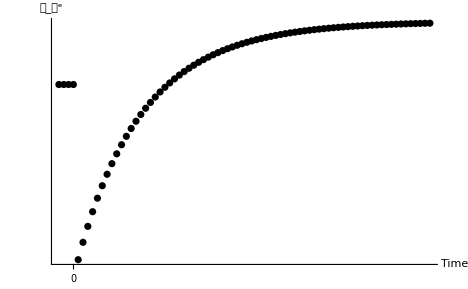

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/cPathAfterThetaDrop.xxx

```mathematica
cPathAfterThetaDrop=Show[𝒸PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝒸_𝓉^e"}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["cPathAfterThetaDrop",TractableFigDir];
```

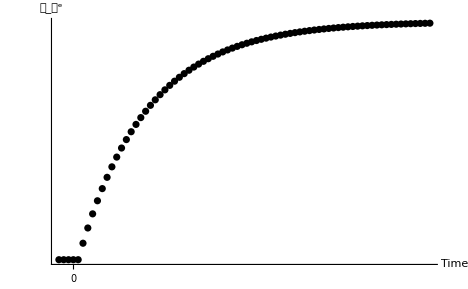

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/mPathAfterThetaDrop.xxx

```mathematica
mPathAfterThetaDrop=Show[𝓂PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝓂_𝓉^e"}
,PlotRange->{{-3,HowMany},{0,Automatic}}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["mPathAfterThetaDrop",TractableFigDir];
```

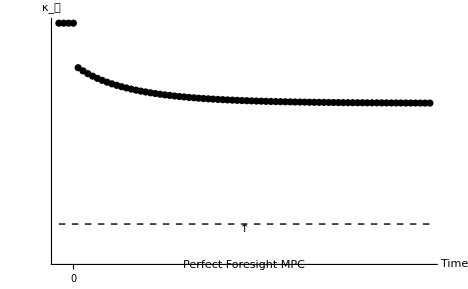

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/MPCPathAfterThetaDrop.xxx

```mathematica
MPCPathAfterThetaDrop=Show[MPCPathPlot
,Graphics[{Dashing[{0.01}],Line[{{timePath[[1]],κ},{timePath[[-1]],κ}}]}]
,Graphics[Text["↑",{(timePath[[1]]+timePath[[-1]])/2,κ},{0,1}]]
,Graphics[Text["Perfect Foresight MPC",{(timePath[[1]]+timePath[[-1]])/2,κ(4/5)},{0,1}]]
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","κ_𝓉"}
,PlotRange->All
,AxesOrigin->{-3,0.}];
ExportFigsToDir["MPCPathAfterThetaDrop",TractableFigDir];
```

```mathematica
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;𝓂EBase=𝓂E;𝒸EBase=𝒸E;
```

Solving ...

Below 𝓂MinPermitted after 43 backwards Euler iterations.

Last 2 Points:(1.80841 | 0.593991 | 0.20245 | -17.0137 | -0.0737916
1.25759 | 0.468788 | 0.257575 | -18.9731 | -0.13305)

Solving ...

Above 𝓂MaxPermitted after 68 backwards Euler iterations.

Last 2 Points:(21.4377 | 2.45831 | 0.0737605 | -6.21838 | -0.000637774
22.4767 | 2.53461 | 0.0731271 | -6.05163 | -0.000582708)

```mathematica
{𝓂Max,𝓂MaxMax}={1.5,5} 𝓂E;
𝒸LowerPlot=Plot[cE[𝓂],{𝓂,0,𝓂Max},PlotStyle->Dashing[{.01}]];
cEPFPlot = Plot[cEPF[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Dashing[{.02}]];
Degree45 = Plot[𝓂,{𝓂,0,cE[𝓂MaxMax]},PlotStyle->Dashing[{.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Black];
BufferFigOrig=Show[Plot[Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂E,2.1 𝓂E}
,Ticks->{{{𝓂E,"(𝓂̌)^e"}},{{𝔤+℧,"γ"},{((r)-ϑ)/ρ,Style["ρ^-1(r-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMax}}
]
(*,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMax}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMax}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂E,𝔤+℧}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.1 𝓂E,((r)-ϑ)/ρ}}]}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMax}}
]
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
];
```

```mathematica
Stable𝓂LocusOrigPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂MaxMax},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];

℧=3 ℧Base;
FindStableArm;
cFuncPlotNew=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->RGBColor[0,0,0]];
cFuncPlotNewPoints=Map[{{#,𝒸[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.01}]];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂MaxMax},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];
Stable𝓂LocusPoints=Map[{{#,𝓂EDelEqZero[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.1}]];
```

Solving ...

Below 𝓂MinPermitted after 54 backwards Euler iterations.

Last 2 Points:(1.83679 | 0.44739 | 0.164496 | -23.1802 | -0.0456878
1.1445 | 0.319712 | 0.20948 | -27.955 | -0.0904325)

Solving ...

Above 𝓂MaxPermitted after 77 backwards Euler iterations.

Last 2 Points:(29.3323 | 2.76707 | 0.0697763 | -5.6131 | -0.000308011
30.7948 | 2.86879 | 0.0693457 | -5.42887 | -0.00028145)

```mathematica
SimGeneratePath[𝓂EBase,100];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{Black,PointSize[0.007]}];
{𝓂MinNew,𝓂MaxNew}={0,5};
{𝒸MinNew,𝒸MaxNew}={0,1.5};
TractableBufferStockTarget = Show[cFuncPlotBase,Stable𝓂LocusPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ Sustainable 𝒸",{𝓂E,0.98𝒸E},{-1,0}]]
,Graphics[Text["c(𝓂) ⟶",{0.7𝓂EBase,0.85𝒸EBase},{1,0}]]
,Ticks->None
,PlotRange->{{𝓂MinNew,𝓂MaxNew},{𝒸MinNew,𝒸MaxNew}}
,AxesLabel->{"𝓂","𝒸"}];
OldAndNewcFuncsPlot = Show[Stable𝓂LocusPlot,cFuncPlotBase,cFuncPlotNew
,PlotRange->{{0,𝓂MaxMax},{0,Automatic}}
,AxesOrigin->{0.,0.}
];
```

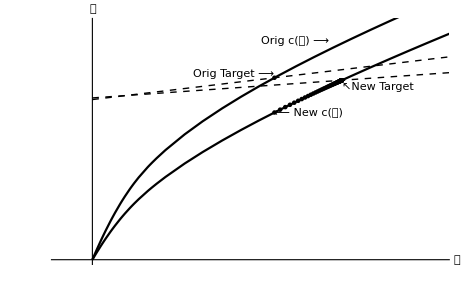

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/PhaseDiagramIncreaseMhoPlot.xxx

```mathematica
PhaseDiagramIncreaseMhoPlot = Show[OldAndNewcFuncsPlot,𝓂𝒸PathPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Orig Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["↖New Target",{𝓂E,0.96𝒸E},{-1,0}]]
,Graphics[Text["Orig c(𝓂) ⟶",{1.3𝓂EBase,1.2𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ New c(𝓂)",{𝓂EBase,cE[𝓂EBase]},{-1,0}]]
,Ticks->None
,AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{𝓂MinNew-1,𝓂E+3},{𝒸MinNew,1.3𝒸EBase}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["PhaseDiagramIncreaseMhoPlot",TractableFigDir];
```

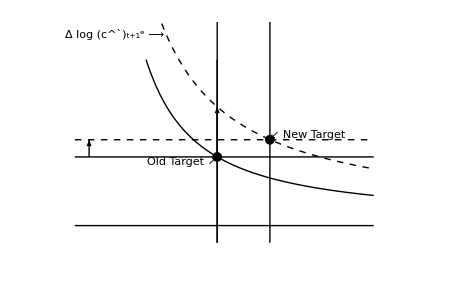

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/cGroIncreaseMhoPlot.xxx

```mathematica
cEModLevtp1=SubsuperscriptBox[OverscriptBox[Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"],"`"],Style["t+1",Plain],Style["e",Plain]];
BufferFigNew = Plot[
Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂EBase,2.1 𝓂EBase}
,PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
cGroIncreaseMhoPlot=Show[BufferFigOrig
,BufferFigNew
(*,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cEModLevtp1}]],{(𝓂EBase 14)/8,Log[𝒞tp1O𝒞t[(𝓂EBase 13)/8]]},{-1,0}]]*)
,Graphics[Text[DisplayForm[RowBox[{dLog, cEModLevtp1,ArrowPointingRight}]],{(𝓂EBase 7.5)/12,Log[𝒞tp1O𝒞t[(𝓂EBase 7.5)/12]]},{1,1}]]
,Graphics[{Dashing[{}],Thickness[Small],Line[{{𝓂E,HorizAxis},{𝓂E,Log[𝒞tp1O𝒞t[1.5]]}}]}]
(*,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.0 𝓂EBase,((r)-ϑ)/ρ}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂EBase,HorizAxis},{𝓂EBase,Log[𝒞tp1O𝒞t[1.5]]}}]}]
,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂EBase,𝔤+℧}}]}]
(*,Graphics[Text[" {",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text["℧(1+ω∇_(t + 1) )∇_(t + 1)    ",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text[" }",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
(*,Graphics[Text["℧^`(1+ω(∇^`)_(t + 1))(∇^`)_(t + 1)",{𝓂E 1.85,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
,Graphics[Text["Old Target ↗",{𝓂EBase,𝔤+℧Base},{1,1}]]
,Graphics[Text[" ↙ New Target",{𝓂E,𝔤+℧},{-1,-1}]]
,Graphics[{PointSize[0.015],Point[{𝓂EBase,𝔤+℧Base}]}]
,Graphics[{PointSize[0.015],Point[{𝓂E,𝔤+℧}]}]
,PhaseArrow[{0.1 𝓂EBase,𝔤+℧Base},{0.1 𝓂EBase,𝔤+℧}]
,PhaseArrow[{𝓂EBase,𝔤+℧Base},{𝓂EBase,Log[𝒞tp1O𝒞t[𝓂EBase]]}]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉","Growth"}
,AxesOrigin->{Automatic,HorizAxis}
,Ticks->{{{𝓂EBase,"m̌"}
,{𝓂E,"(𝓂̌)^`"}}
,{{𝔤+℧Base,"γ"}
,{𝔤+℧,"γ^`"}
,{(rBase-ϑ)/ρ,Style["ρ^-1(𝓇-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}
(*,{((r)-ϑ)/ρ,Style["ρ^-1(𝓇^`-ϑ)≈þ^`",CharacterEncoding->"WindowsANSI"]}*)
}}
(*,PlotRange->{{0,2.6 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.5𝓂E]]}}*)
,PlotRange->{{0,1.8 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.45𝓂E]]}}
];
ExportFigsToDir["cGroIncreaseMhoPlot",TractableFigDir];
```

```mathematica
HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path][[1]],HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path][[2]],HowMany];
MPCPath=Map[cE'[#]&,Rest[𝓂Path]];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot = ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot = ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot = ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];
```

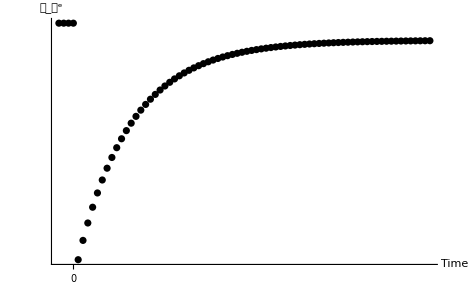

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/cPathAfterMhoRise.xxx

```mathematica
cPathAfterMhoRise=Show[𝒸PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝒸_𝓉^e"}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["cPathAfterMhoRise",TractableFigDir];
```

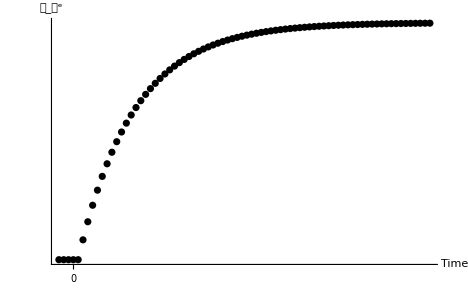

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/mPathAfterMhoRise.xxx

```mathematica
mPathAfterMhoRise=Show[𝓂PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝓂_𝓉^e"}
,PlotRange->{{-3,HowMany},{0,Automatic}}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["mPathAfterMhoRise",TractableFigDir];
```

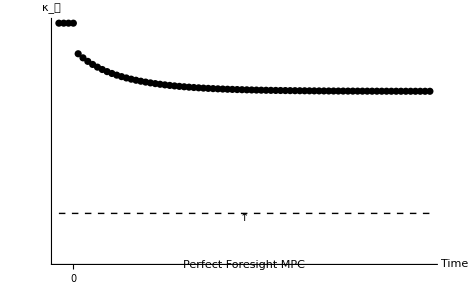

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/MPCPathAfterMhoRise.xxx

```mathematica
MPCPathAfterMhoRise=Show[MPCPathPlot
,Graphics[{Dashing[{0.01}],Line[{{timePath[[1]],κ},{timePath[[-1]],κ}}]}]
,Graphics[Text["↑",{(timePath[[1]]+timePath[[-1]])/2,κ},{0,1}]]
,Graphics[Text["Perfect Foresight MPC",{(timePath[[1]]+timePath[[-1]])/2,κ(4/5)},{0,1}]]
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","κ_𝓉"}
,PlotRange->All
,AxesOrigin->{-3,0.}];
ExportFigsToDir["MPCPathAfterMhoRise",TractableFigDir];
```

```mathematica
(* Now decrease expected income growth *)
Get[CoreCodeDir<>"/ParametersBase.m"];
FindStableArm;κEBase = κE;𝓂EBase=𝓂E;𝒸EBase=𝒸E;
```

Solving ...

Below 𝓂MinPermitted after 43 backwards Euler iterations.

Last 2 Points:(1.80841 | 0.593991 | 0.20245 | -17.0137 | -0.0737916
1.25759 | 0.468788 | 0.257575 | -18.9731 | -0.13305)

Solving ...

Above 𝓂MaxPermitted after 68 backwards Euler iterations.

Last 2 Points:(21.4377 | 2.45831 | 0.0737605 | -6.21838 | -0.000637774
22.4767 | 2.53461 | 0.0731271 | -6.05163 | -0.000582708)

```mathematica
{𝓂Max,𝓂MaxMax}={1.5,5} 𝓂E;
𝒸LowerPlot=Plot[cE[𝓂],{𝓂,0,𝓂Max},PlotStyle->Dashing[{.01}]];
cEPFPlot = Plot[cEPF[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Dashing[{.02}]];
Degree45 = Plot[𝓂,{𝓂,0,cE[𝓂MaxMax]},PlotStyle->Dashing[{.01}]];
cFuncPlotBase=cFuncPlot=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->Black];
BufferFigOrig=Show[Plot[Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂E,2.1 𝓂E}
,Ticks->{{{𝓂E,"(𝓂̌)^e"}},{{𝔤+℧,"γ"},{((r)-ϑ)/ρ,Style["ρ^-1(r-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}}}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMax}}
]
(*,Graphics[{Dashing[{0.005,0.025}],Thickness[Medium],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMax}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂E,HorizAxis},{𝓂E,𝒸GroMax}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂E,𝔤+℧}}]}]
,Graphics[{Dashing[{}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.1 𝓂E,((r)-ϑ)/ρ}}]}
,PlotRange->{{0,2.1 𝓂E},{HorizAxis,𝒸GroMax}}
]
,AxesOrigin->{((r)-ϑ)/ρ-0.1,HorizAxis}
];
```

```mathematica
Stable𝓂LocusOrigPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂MaxMax},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];

𝔤   =-0.02;

FindStableArm;
cFuncPlotNew=Plot[cE[𝓂],{𝓂,0,𝓂MaxMax},PlotStyle->RGBColor[0,0,0]];
cFuncPlotNewPoints=Map[{{#,𝒸[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.01}]];
Stable𝓂LocusPlot=Plot[{𝓂EDelEqZero[𝓂]},{𝓂,0,𝓂MaxMax},PlotStyle->{Black,Dashing[{.01}],Thickness[Medium]}];
Stable𝓂LocusPoints=Map[{{#,𝓂EDelEqZero[#]}}&,Table[𝓂,{𝓂,0,𝓂MaxMax,0.1}]];
```

Solving ...

Below 𝓂MinPermitted after 107 backwards Euler iterations.

Last 2 Points:(1.823 | 0.580623 | 0.187582 | -19.1097 | -0.0728097
1.24371 | 0.456724 | 0.246514 | -21.2704 | -0.138897)

Solving ...

Above 𝓂MaxPermitted after 164 backwards Euler iterations.

Last 2 Points:(34.4497 | 3.11925 | 0.0640472 | -5.20355 | -0.000159208
35.15 | 3.16406 | 0.0639383 | -5.13261 | -0.000151844)

```mathematica
SimGeneratePath[𝓂EBase,100];
𝓂𝒸PathPlot = ListPlot[𝓂𝒸Path,PlotStyle->{Black,PointSize[0.007]}];
{𝓂MinNew,𝓂MaxNew}={0,5};
{𝒸MinNew,𝒸MaxNew}={0,1.5};
TractableBufferStockTarget = Show[cFuncPlotBase,Stable𝓂LocusPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ Sustainable 𝒸",{𝓂E,0.98𝒸E},{-1,0}]]
,Graphics[Text["c(𝓂) ⟶",{0.7𝓂EBase,0.85𝒸EBase},{1,0}]]
,Ticks->None
,PlotRange->{{𝓂MinNew,𝓂MaxNew},{𝒸MinNew,𝒸MaxNew}}
,AxesLabel->{"𝓂","𝒸"}];
OldAndNewcFuncsPlot = Show[Stable𝓂LocusPlot,cFuncPlotBase,cFuncPlotNew
,PlotRange->{{0,𝓂MaxMax},{0,Automatic}}
,AxesOrigin->{0.,0.}
];
```

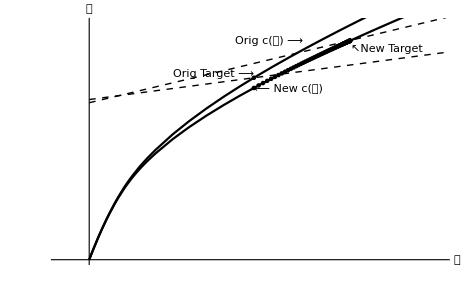

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/PhaseDiagramAfterGFallPlot.xxx

```mathematica
PhaseDiagramAfterGFallPlot = Show[OldAndNewcFuncsPlot,𝓂𝒸PathPlot,Stable𝓂LocusOrigPlot
,Graphics[Text["Orig Target ⟶",{𝓂EBase,1.02𝒸EBase},{1,0}]]
,Graphics[Text["↖New Target",{𝓂E,0.96𝒸E},{-1,0}]]
,Graphics[Text["Orig c(𝓂) ⟶",{1.3𝓂EBase,1.2𝒸EBase},{1,0}]]
,Graphics[Text[" ⟵ New c(𝓂)",{𝓂EBase,cE[𝓂EBase]},{-1,0}]]
,Ticks->None
,AxesLabel->{"𝓂","𝒸"}
,PlotRange->{{𝓂MinNew-1,𝓂E+3},{𝒸MinNew,1.3𝒸EBase}}
,AxesOrigin->{0.,0.}
];
ExportFigsToDir["PhaseDiagramAfterGFallPlot",TractableFigDir];
```

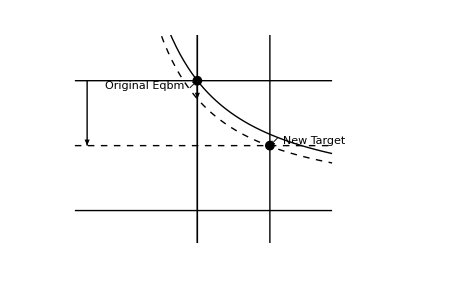

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/cGroAfterGFallPlot.xxx

```mathematica
cEModLevtp1=SubsuperscriptBox[OverscriptBox[Style["c",{Bold,Italic},CharacterEncoding->"WindowsANSI"],"`"],Style["t+1",Plain],Style["e",Plain]];
BufferFigNew = Plot[
Log[𝒞tp1O𝒞t[𝓂]],{𝓂,0.5 𝓂EBase,2.1 𝓂EBase}
,PlotStyle->{Dashing[{.01}],Thickness[Medium],Black}];
cGroAfterGFallPlot=Show[BufferFigOrig
,BufferFigNew
(*,Graphics[Text[DisplayForm[RowBox[{ArrowPointingLeft,dLog,cEModLevtp1}]],{(𝓂EBase 14)/8,Log[𝒞tp1O𝒞t[(𝓂EBase 13)/8]]},{-1,0}]]*)
,Graphics[Text[DisplayForm[RowBox[{dLog, cEModLevtp1,ArrowPointingRight}]],{(𝓂EBase 7.5)/12,Log[𝒞tp1O𝒞t[(𝓂EBase 7.5)/12]]},{1,1}]]
,Graphics[{Dashing[{}],Thickness[Small],Line[{{𝓂E,HorizAxis},{𝓂E,Log[𝒞tp1O𝒞t[1.5]]}}]}]
(*,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,((r)-ϑ)/ρ},{2.0 𝓂EBase,((r)-ϑ)/ρ}}]}]*)
,Graphics[{Dashing[{}],Thickness[Small],Black,Line[{{𝓂EBase,HorizAxis},{𝓂EBase,Log[𝒞tp1O𝒞t[1.5]]}}]}]
,Graphics[{Dashing[{0.01}],Thickness[Medium],Line[{{0,𝔤+℧},{2.1 𝓂EBase,𝔤+℧}}]}]
(*,Graphics[Text[" {",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text["℧(1+ω∇_(t + 1) )∇_(t + 1)    ",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)-0.003},{1,0}]]*)
(*,Graphics[Text[" }",{𝓂E 1.65,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
(*,Graphics[Text["℧^`(1+ω(∇^`)_(t + 1))(∇^`)_(t + 1)",{𝓂E 1.85,1/2 (Log[𝒞tp1O𝒞t[𝓂E 2]]+((r)-ϑ)/ρ)+0.001},{-1,0}]]*)
,Graphics[Text["Original Eqbm ↗",{𝓂EBase,𝔤Base+℧},{1,1}]]
,Graphics[Text[" ↙ New Target",{𝓂E,𝔤+℧},{-1,-1}]]
,Graphics[{PointSize[0.015],Point[{𝓂EBase,𝔤Base+℧}]}]
,Graphics[{PointSize[0.015],Point[{𝓂E,𝔤+℧}]}]
,PhaseArrow[{0.1 𝓂EBase,𝔤Base+℧},{0.1 𝓂EBase,𝔤+℧}]
,PhaseArrow[{𝓂EBase,𝔤Base+℧},{𝓂EBase,Log[𝒞tp1O𝒞t[𝓂EBase]]}]
,Axes->{Automatic,Automatic}
,AxesLabel->{"𝓂_𝓉","Growth"}
,AxesOrigin->{Automatic,HorizAxis}
,Ticks->{{{𝓂EBase,"m̌"}
,{𝓂E,"(𝓂̌)^`"}}
,{{𝔤Base+℧,"γ"}
,{𝔤+℧,"γ^`"}
,{(rBase-ϑ)/ρ,Style["ρ^-1(𝓇-ϑ)≈þ",CharacterEncoding->"WindowsANSI"]}
(*,{((r)-ϑ)/ρ,Style["ρ^-1(𝓇^`-ϑ)≈þ^`",CharacterEncoding->"WindowsANSI"]}*)
}}
(*,PlotRange->{{0,2.6 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.5𝓂E]]}}*)
,PlotRange->{{0,1.8 𝓂E},{HorizAxis,Log[𝒞tp1O𝒞t[0.45𝓂E]]}}
];
ExportFigsToDir["cGroAfterGFallPlot",TractableFigDir];
```

```mathematica
HowMany=75;
𝓂Path=Take[Transpose[𝓂𝒸Path][[1]],HowMany];
𝒸Path=Take[Transpose[𝓂𝒸Path][[2]],HowMany];
MPCPath=Map[cE'[#]&,Rest[𝓂Path]];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[𝓂Path,𝓂EBase];
PrependTo[𝒸Path,𝒸EBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
PrependTo[MPCPath,κEBase];
timePath=Table[i,{i,Length[𝒸Path]}];
𝒸PathPlot = ListPlot[Transpose[{timePath,𝒸Path}],PlotRange->All];
𝓂PathPlot = ListPlot[Transpose[{timePath,𝓂Path}],PlotRange->All];
MPCPathPlot = ListPlot[Transpose[{timePath,MPCPath}],PlotRange->All];
```

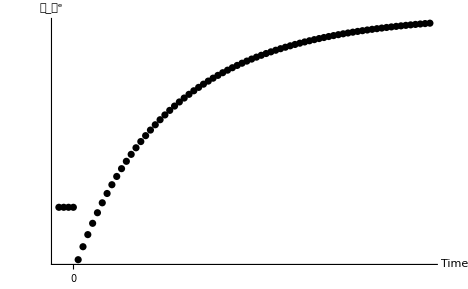

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/cPathAfterGFall.xxx

```mathematica
cPathAfterGFall=Show[𝒸PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝒸_𝓉^e"}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["cPathAfterGFall",TractableFigDir];
```

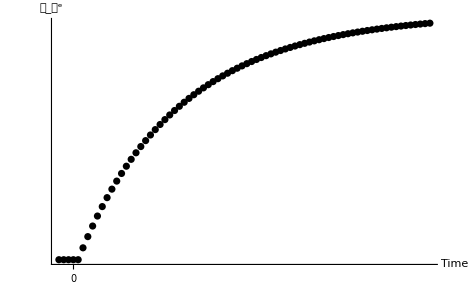

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/mPathAfterGFall.xxx

```mathematica
mPathAfterGFall=Show[𝓂PathPlot
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","𝓂_𝓉^e"}
,PlotRange->{{-3,HowMany},{0,Automatic}}
,AxesOrigin->{-3,0}
,PlotRange->{{-3,Automatic},{0,Automatic}}
];
ExportFigsToDir["mPathAfterGFall",TractableFigDir];
```

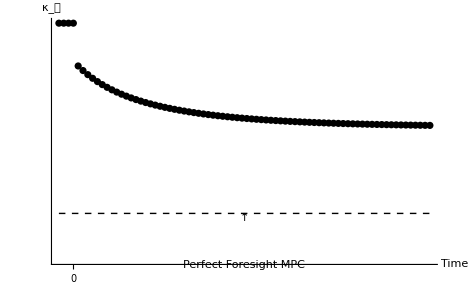

Exporting figure to /Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/TractableBufferStock/Figures/MPCPathAfterGFall.xxx

```mathematica
MPCPathAfterGFall=Show[MPCPathPlot
,Graphics[{Dashing[{0.01}],Line[{{timePath[[1]],κ},{timePath[[-1]],κ}}]}]
,Graphics[Text["↑",{(timePath[[1]]+timePath[[-1]])/2,κ},{0,1}]]
,Graphics[Text["Perfect Foresight MPC",{(timePath[[1]]+timePath[[-1]])/2,κ(4/5)},{0,1}]]
,Ticks->{{{4,"0"}},None}
,AxesLabel->{"Time","κ_𝓉"}
,PlotRange->All
,AxesOrigin->{-3,0.}];
ExportFigsToDir["MPCPathAfterGFall",TractableFigDir];
```